# Superconducting qubits Hub

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

frequency unit: MHz
time unit: μs

```mathematica
Options[SuperconductingHub]={
(* The number of qubits should match all assignments. Qubits are numbered from 0 to N-1 *)
qubitsNum->6,
(* The T1 time *)
T1-><|0->63,1->93,2->109,3->115,4->68,5->125|>,
(* The T2 time with Hahn echo applied *)
T2-><|0->113,1->149,2->185,3->161,4->122,5->200|>,
(* Excited population probability in the initialisation, also the thermal state *)
ExcitedInit-><|0->0.032,1->0.021,2->0.008,3->0.009,4->0.025,5->0.007|>,
(* Each qubit frequency in MHz   *)
QubitFreq-><|0->4500,1->4900,2->4700,3->5100,4->4900,5->5300|>,
(* Exchange coupling strength of the resonators. Use [Esc]o-o[Esc] for notation *)
ExchangeCoupling-><|0<->1->4,0<->2->1.5,1<->3->1.5,2<->3->4,2<->4->1.5,3<->5->1.5,4<->5->4|>,
(* Transmon Anharmonicity in MHz *)
Anharmonicity-><|0->296.7,1->298.6,2->297.4,3->298.3,4->297.2,5->299.1|>,
(* Fidelity of qubit readout *)
FidRead-><|0->0.9,1->0.92,2->0.96,3->0.97,4->0.93,5->0.97|>,
(* Measurement duration in μs. It is done without quantum amplifiers *)
DurMeas->5,
(* Duration of the Rx and Ry gates are the same regardless the angle. Rz is virtual and perfect. *)
DurRxRy->0.05,
(* Duration of the cross resonance ZX gate that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZX->0.5,
(* Duration of the sizzle gate is fixed regardless the angle that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZZ->0.5,
(* switches to turn/off some noise*)
StdPassiveNoise->True,
ZZPassiveNoise->True
};
```

```mathematica
dev=SuperconductingHub[];
```

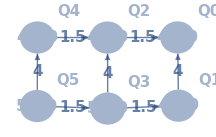

```mathematica
g=dev[Connectivity]
```

## Passive noise

### Simple test

```mathematica
noisycirc=
InsertCircuitNoise[{Sequence@@(Subscript[Init, #]&/@Range[0,5]),Subscript[Rx, 0][π],Subscript[Rx, 1][π],Subscript[Rx, 3][π/2],Subscript[ZX, 1,0],Subscript[ZZ, 4,5],Subscript[Rx, 0][π/4],Subscript[Rx, 1][π],Subscript[Rx, 2][π],Subscript[ZX, 2,0]},SuperconductingHub[]];
```

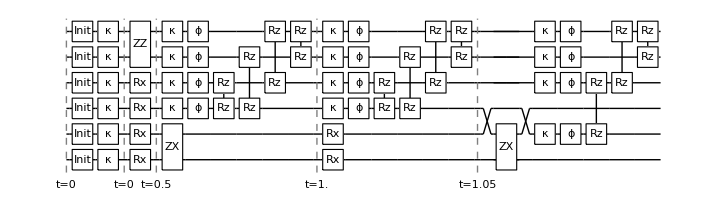

```mathematica
DrawCircuit[noisycirc]
```

### Initialisation

```mathematica
DestroyAllQuregs[];
ρinit=CreateDensityQureg[6];
ρ=CreateDensityQureg[6];
```

```mathematica
Values@OptionValue[SuperconductingHub,ExcitedInit]
```

{0.032,0.021,0.008,0.009,0.025,0.007}

```mathematica
noisycirc=InsertCircuitNoise[Subscript[Init, #]&/@Range[0,5],SuperconductingHub[],ReplaceAliases->True]
```

{{0,{Kraus_0[{{{0.98387,0.},{0.,0.}},{{0.,0.98387},{0.,0.}},{{0.,0.},{0.,0.178885}},{{0.,0.},{0.178885,0.}}}],Kraus_1[{{{0.989444,0.},{0.,0.}},{{0.,0.989444},{0.,0.}},{{0.,0.},{0.,0.144914}},{{0.,0.},{0.144914,0.}}}],Kraus_2[{{{0.995992,0.},{0.,0.}},{{0.,0.995992},{0.,0.}},{{0.,0.},{0.,0.0894427}},{{0.,0.},{0.0894427,0.}}}],Kraus_3[{{{0.99549,0.},{0.,0.}},{{0.,0.99549},{0.,0.}},{{0.,0.},{0.,0.0948683}},{{0.,0.},{0.0948683,0.}}}],Kraus_4[{{{0.987421,0.},{0.,0.}},{{0.,0.987421},{0.,0.}},{{0.,0.},{0.,0.158114}},{{0.,0.},{0.158114,0.}}}],Kraus_5[{{{0.996494,0.},{0.,0.}},{{0.,0.996494},{0.,0.}},{{0.,0.},{0.,0.083666}},{{0.,0.},{0.083666,0.}}}]},{}}}

```mathematica
(* initialise matrix as a random mix state, then apply the initialisation command *)
SetQuregMatrix[ρinit,RandomMixState[6]];
```

```mathematica
ApplyCircuit[ρinit,ExtractCircuit@noisycirc];
Diagonal@Re@GetQuregMatrix[ρinit]
```

{0.901981,0.0298175,0.0193479,0.0006396,0.00727404,0.000240464,0.000156031,5.15806×10^-6,0.00819155,0.000270795,0.000175713,5.80868×10^-6,0.0000660609,2.18383×10^-6,1.41704×10^-6,4.68442×10^-8,0.0231277,0.000764552,0.0004961,0.0000164,0.000186514,6.16575×10^-6,4.00081×10^-6,1.32258×10^-7,0.00021004,6.94346×10^-6,4.50545×10^-6,1.4894×10^-7,1.69387×10^-6,5.59957×10^-8,3.63343×10^-8,1.20113×10^-9,0.00635837,0.000210194,0.00013639,4.50876×10^-6,0.0000512772,1.69511×10^-6,1.09992×10^-6,3.6361×10^-8,0.0000577451,1.90893×10^-6,1.23866×10^-6,4.09474×10^-8,4.65686×10^-7,1.53946×10^-8,9.98918×10^-9,3.30221×10^-10,0.000163035,5.38959×10^-6,3.49718×10^-6,1.15609×10^-7,1.3148×10^-6,4.34645×10^-8,2.82031×10^-8,9.32333×10^-10,1.48064×10^-6,4.89469×10^-8,3.17605×10^-8,1.04993×10^-9,1.19407×10^-8,3.94733×10^-10,2.56133×10^-10,8.4672×10^-12}

```mathematica
(* Expected diagonals *)
Reverse@Diagonal[KroneckerProduct@@({{#,0},{0,1-#}}&/@(Values@OptionValue[SuperconductingHub,ExcitedInit]))]
```

{0.901981,0.00635837,0.0231277,0.000163035,0.00819155,0.0000577451,0.00021004,1.48064×10^-6,0.00727404,0.0000512772,0.000186514,1.3148×10^-6,0.0000660609,4.65686×10^-7,1.69387×10^-6,1.19407×10^-8,0.0193479,0.00013639,0.0004961,3.49718×10^-6,0.000175713,1.23866×10^-6,4.50545×10^-6,3.17605×10^-8,0.000156031,1.09992×10^-6,4.00081×10^-6,2.82031×10^-8,1.41704×10^-6,9.98918×10^-9,3.63343×10^-8,2.56133×10^-10,0.0298175,0.000210194,0.000764552,5.38959×10^-6,0.000270795,1.90893×10^-6,6.94346×10^-6,4.89469×10^-8,0.000240464,1.69511×10^-6,6.16575×10^-6,4.34645×10^-8,2.18383×10^-6,1.53946×10^-8,5.59957×10^-8,3.94733×10^-10,0.0006396,4.50876×10^-6,0.0000164,1.15609×10^-7,5.80868×10^-6,4.09474×10^-8,1.4894×10^-7,1.04993×10^-9,5.15806×10^-6,3.6361×10^-8,1.32258×10^-7,9.32333×10^-10,4.68442×10^-8,3.30221×10^-10,1.20113×10^-9,8.4672×10^-12}

### Thermal state

Assume ρinit is initialised to the initial state

```mathematica
noisycirc=InsertCircuitNoise[{Subscript[Wait, #][1]&/@Range[0,5]},SuperconductingHub[],ReplaceAliases->True]
```

{{0,{Kraus_0[{{{0.98387,0.},{0.,0.976092}},{{0.,0.123466},{0.,0.}},{{0.177471,0.},{0.,0.178885}},{{0.,0.},{0.0224483,0.}}}],Deph_0[0.00440526],Kraus_1[{{{0.989444,0.},{0.,0.984139}},{{0.,0.102325},{0.,0.}},{{0.144137,0.},{0.,0.144914}},{{0.,0.},{0.0149866,0.}}}],Deph_1[0.00334447],R[0.131923,Z_0 Z_1],Kraus_2[{{{0.995992,0.},{0.,0.991434}},{{0.,0.0951803},{0.,0.}},{{0.0890334,0.},{0.,0.0894427}},{{0.,0.},{0.00854745,0.}}}],Deph_2[0.00269541],R[-0.0277977,Z_0 Z_2],Kraus_3[{{{0.99549,0.},{0.,0.991171}},{{0.,0.0926285},{0.,0.}},{{0.0944568,0.},{0.,0.0948683}},{{0.,0.},{0.00882732,0.}}}],Deph_3[0.00309597],R[-0.0273321,Z_1 Z_3],R[0.133003,Z_2 Z_3],Kraus_4[{{{0.987421,0.},{0.,0.980187}},{{0.,0.119303},{0.,0.}},{{0.156956,0.},{0.,0.158114}},{{0.,0.},{0.0191038,0.}}}],Deph_4[0.00408161],R[-0.0276241,Z_2 Z_4],Kraus_5[{{{0.996494,0.},{0.,0.992516}},{{0.,0.0889512},{0.,0.}},{{0.083332,0.},{0.,0.083666}},{{0.,0.},{0.00746837,0.}}}],Deph_5[0.00249376],R[-0.0274045,Z_3 Z_5],R[0.132693,Z_4 Z_5]},{}}}

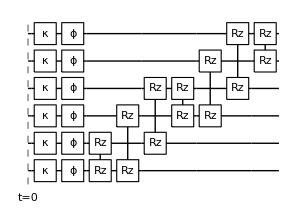

```mathematica
DrawCircuit[noisycirc]
```

```mathematica
δt=4;
dev=SuperconductingHub[];
SetQuregMatrix[ρ,RandomMixState[6]];
data=Table[
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[Subscript[Wait, #][δt]&/@Range[0,5],dev,ReplaceAliases->True]];
{t,CalcFidelityDensityMatrices[ρ,ρinit]}
,{t,δt,440,δt}];
```

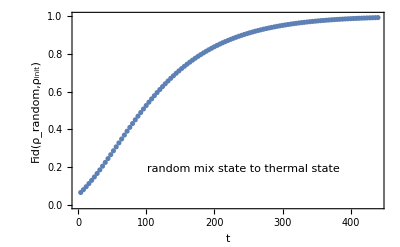

```mathematica
ListPlot[data,PlotRange->{Automatic,{0,1}},Frame->True,FrameLabel->{"t","Fid(ρ_random,ρ_init)"},FrameStyle->Directive[Black,Thick],ImageSize->400,BaseStyle->{17},Epilog->Inset["random mix state to thermal state",Scaled[{0.55,0.2}]]]
```

### T1 experiment

```mathematica
δt=4;
SetQuregMatrix[ρ,RandomMixState[6]];
dataT1=Table[
dev=SuperconductingHub[];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[Subscript[Init, #]&/@Range[0,5],dev,ReplaceAliases->True]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[Subscript[Rx, #][π]&/@Range[0,5],dev,ReplaceAliases->True]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[Subscript[Wait, #][t]&/@Range[0,5],dev,ReplaceAliases->True]];
{t,CalcProbOfOutcome[ρ,#,1]}&/@Range[0,5]
,{t,0,500,δt}];
```

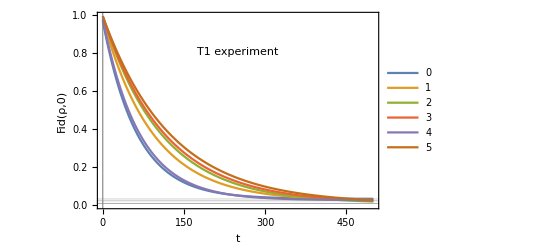

```mathematica
excp=Values@OptionValue[SuperconductingHub,ExcitedInit];
ListPlot[Transpose[dataT1],Frame->True,PlotLegends->Placed[Range[0,5],{0.9,0.5}],GridLines->{excp},Frame->True,FrameLabel->{"t","Fid(ρ,0)"},FrameStyle->Directive[Black,Thick],ImageSize->400,BaseStyle->{17},Epilog->Inset["T1 experiment",Scaled[{0.5,0.8}]],Joined->True]
```

### T2 experiment

```mathematica
δt=4;
SetQuregMatrix[ρ,RandomMixState[6]];
dataT2=Table[
dev=SuperconductingHub[];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[Subscript[Init, #]&/@Range[0,5],dev,ReplaceAliases->True]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[Flatten[Subscript[Ry, #][π/2]&/@Range[0,5]],dev,ReplaceAliases->True]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[Subscript[Wait, #][t]&/@Range[0,5],dev,ReplaceAliases->True]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[Flatten[Subscript[Ry, #][-π/2]&/@Range[0,5]],dev,ReplaceAliases->True]];
{t,CalcProbOfOutcome[ρ,#,0]}&/@Range[0,5]
,{t,0,500,δt}];
```

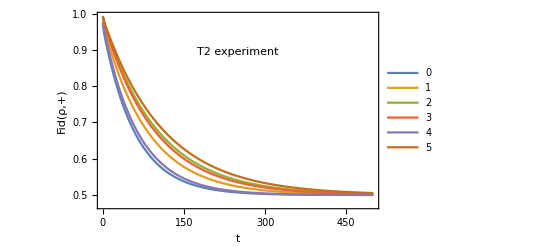

```mathematica
ListPlot[Transpose[dataT2],PlotLegends->Placed[Range[0,5],{0.9,0.55}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,Thick],ImageSize->400,FrameLabel->{"t","Fid(ρ,+)"},BaseStyle->{17},Epilog->Inset["T2 experiment",Scaled[{0.5,0.8}]],Joined->True]
```

## VQE of H_2 on SQC device

```mathematica
H2onSQC<<"VQEonSQC/H2onSQC.mx";
```

```mathematica
H2=ImageResize[MoleculePlot3D[Molecule[ConstantArray["H",2],Bond[{#,#+1},"Single"]&/@Range[1],AtomCoordinates->({.8*#,0,0}&/@Range[0,1])]],200]
```

-Graphics-

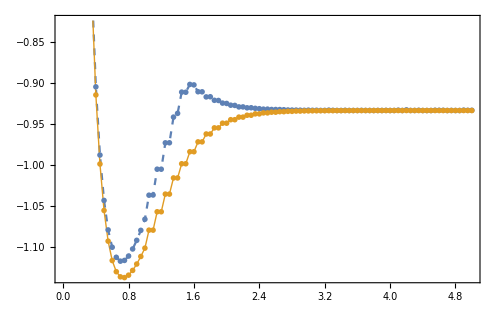

/home/cica/vqd/img/vqeh2.pdf

```mathematica
ListPlot[{Values@H2onSQC[[All,{"description","cost"}]],Values@H2onSQC[[All,{"description","groundstate"}]]},Joined->{True, True},PlotStyle->{Dashed,Thick},Frame->True,PlotMarkers->{"OpenMarkers",5},FrameStyle->Directive[Black,Thick,FontFamily->"Serif",FontSize->17],Epilog->Inset[H2,Scaled[{0.8,0.8}]],
PlotLegends->Placed[LineLegend[{"VQE result","Exact ground state"},Spacings->0.,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0,Background->White]&)],{0.7,0.2}],ImageSize->500]
Export["/home/cica/vqd/img/vqeh2.pdf",%]
```